# e^-e^+→γ γ

## Feynman Diagram

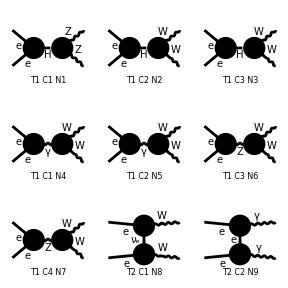

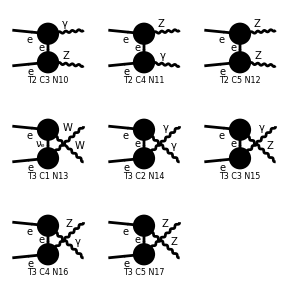

```mathematica
S1=CreateTopologies[0, 2 -> 2];
Diagrams=InsertFields[S1,{-F[2,{1}],F[2,{1}]}->{V{1},V{1}},InsertionLevel->{Classes}];
Paint[%];
```

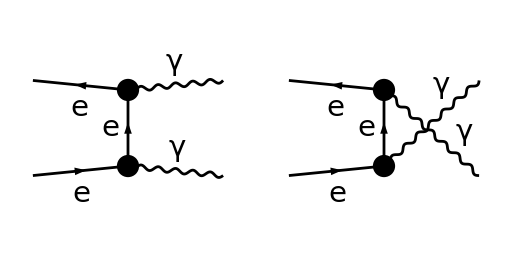

```mathematica
T1=CreateTopologies[0, 2 -> 2];
diagsG = InsertFields[T1, {-F[2, {1}], F[2, {1}]} ->
		{V{1},V{1}}, InsertionLevel -> {Classes},
		Model -> "SM", ExcludeParticles -> {S[1], S[2], V[2],V[3]}];
Paint[diagsG, ColumnsXRows -> {2, 1}, Numbering -> None,SheetHeader->None,ImageSize->{512,256}];
```

## Square amplitude (Momenta)

```mathematica
PairAnni= FCFAConvert[CreateFeynAmp[diagsG, Truncated -> False],
IncomingMomenta->{p,p'},OutgoingMomenta->{k,k'},UndoChiralSplittings->True,
ChangeDimension->4,List->False,SMP->True]
```

-(((ε̄)^*)^Lor1(k) ((ε̄)^*)^Lor2(k') (φ(-p̄,m_e)).(ⅈ e (γ̄)^Lor2).(γ̄·(OverBar[p']-k̄)+m_e).(ⅈ e (γ̄)^Lor1).(φ(OverBar[p'],m_e)))/((k̄-OverBar[p'])^2-m_e^2)-(((ε̄)^*)^Lor1(k) ((ε̄)^*)^Lor2(k') (φ(-p̄,m_e)).(ⅈ e (γ̄)^Lor1).(γ̄·(OverBar[p']-OverBar[k'])+m_e).(ⅈ e (γ̄)^Lor2).(φ(OverBar[p'],m_e)))/((OverBar[k']-OverBar[p'])^2-m_e^2)

```mathematica
ComplexConjugate[PairAnni]
```

(e^2 (ε̄)^Lor1(k) (ε̄)^Lor2(k') (φ(OverBar[p'],m_e)).(γ̄)^Lor1.(γ̄·(OverBar[p']-k̄)+m_e).(γ̄)^Lor2.(φ(-p̄,m_e)))/((k̄-OverBar[p'])^2-m_e^2)+(e^2 (ε̄)^Lor1(k) (ε̄)^Lor2(k') (φ(OverBar[p'],m_e)).(γ̄)^Lor2.(γ̄·(OverBar[p']-OverBar[k'])+m_e).(γ̄)^Lor1.(φ(-p̄,m_e)))/((OverBar[k']-OverBar[p'])^2-m_e^2)

```mathematica
sqAmpPairAnnitest= (PairAnni (ComplexConjugate[PairAnni]//FCRenameDummyIndices))//Expand//DoPolarizationSums[#,k,
		0]&//DoPolarizationSums[#,k',0]&//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		ReplaceAll[#, DiracTrace -> Tr] & // Contract//Simplify
```

PolarizationSum::notmassless: Warning! You are inserting a polarization sum for massless vector bosons, but the momentum of the external boson k is not on-shell. Please put it on-shell via ScalarProduct[k,k]=0

General::stop: Further output of PolarizationSum::notmassless will be suppressed during this calculation.

4 e^4 (-(2 (-2 m_e^2 (OverBar[k']·OverBar[p'])+(k̄·OverBar[k']) (2 (p̄·OverBar[p'])+m_e^2)+m_e^2 (p̄·OverBar[k'])-2 (k̄·OverBar[p']) (p̄·OverBar[p']+m_e^2)+m_e^2 (k̄·p̄)+3 m_e^2 OverBar[p']^2-3 m_e^2 (p̄·OverBar[p'])-2 (p̄·OverBar[p']) (OverBar[k']·OverBar[p'])+2 OverBar[p']^2 (p̄·OverBar[p'])-2 m_e^4))/(((k̄-OverBar[p'])^2-m_e^2) ((OverBar[k']-OverBar[p'])^2-m_e^2))-(1/((OverBar[k']-OverBar[p'])^2-m_e^2))^2 (4 m_e^2 (-OverBar[k']·OverBar[p']+OverBar[k']^2+m_e^2)-2 (p̄·OverBar[k']) (OverBar[k']·OverBar[p']-OverBar[p']^2+2 m_e^2)+(p̄·OverBar[p']) (OverBar[k']^2-OverBar[p']^2+3 m_e^2))+(1/((k̄-OverBar[p'])^2-m_e^2))^2 (4 m_e^2 (k̄·OverBar[p'])+2 (k̄·p̄) (k̄·OverBar[p']-OverBar[p']^2+2 m_e^2)-(k̄)^2 (p̄·OverBar[p']+4 m_e^2)-3 m_e^2 (p̄·OverBar[p'])+OverBar[p']^2 (p̄·OverBar[p'])-4 m_e^4))

```mathematica
masslessElectronssqAmp= (sqAmpPairAnnitest/. {SMP["m_e"] -> 0})//FullSimplify
```

4 e^4 ((4 (p̄·OverBar[p']) (OverBar[k']·OverBar[p']-(k̄·OverBar[k'])+k̄·OverBar[p']-OverBar[p']^2))/((k̄-OverBar[p'])^2 (OverBar[k']-OverBar[p'])^2)+(1/(OverBar[k']-OverBar[p'])^2)^2 (2 (p̄·OverBar[k']) (OverBar[k']·OverBar[p']-OverBar[p']^2)+(OverBar[p']^2-OverBar[k']^2) (p̄·OverBar[p']))+(1/(k̄-OverBar[p'])^2)^2 (2 (k̄·p̄) (k̄·OverBar[p']-OverBar[p']^2)+(OverBar[p']^2-(k̄)^2) (p̄·OverBar[p'])))

```mathematica
ChangeDimension[%,D]
```

4 e^4 ((4 (p·p') (k'·p'-(k·k')+k·p'-p'^2))/((k-p')^2 (k'-p')^2)+(1/(k'-p')^2)^2 (2 (p·k') (k'·p'-p'^2)+(p'^2-k'^2) (p·p'))+(1/(k-p')^2)^2 (2 (k·p) (k·p'-p'^2)+(p'^2-k^2) (p·p')))

## Kinematics

Diagram 1

Incoming Momenta - p (electron), p’(positron)

p^μ=(p^0,p^1,p^2,p^3)
p_e=(E_e, 0, 0, p_e z )
p'_p=(E_p, 0, 0, -p_pz )
Invariant: p_e^2=E_e^2-m_e^2

Outgoing Momenta - k (photon), k’ (photon)

k^μ=(k^0,k^1,k^2,k^3)
k_γ=(E_γ,E_γ sin θ , 0, E_γ cos θ )
k'_γ=(E_γ, -E_γsin θ , 0,- E_γcos θ  )
Invariant: k_γ^2=E_γ^2-m_γ^2

General:
s = ( p^μ+p'^μ )^2 =( k^μ+k'^μ )^2 = (p)^2+(p')^2+2( p*p' ) = (p^0)^2-p^2+(p'^0)^2-p'^2+2 p^0 p'^0-2p p'cos( θ )  

t = ( k^μ-p^μ )^2 = ( k'^μ-p'^μ )^2 = (k)^2+(p)^2-2( k*p ) = (k^0)^2-k^2+(p^0)^2-p^2-2 k^0 p^0+2k p cos( θ )

u = ( k'^μ-p^μ )^2 = ( k^μ-p'^μ )^2 = (k')^2+(p)^2+2( k'*p ) = (k'^0)^2-k'^2+(p^0)^2-p^2-2 k'^0 p^0+2k' p cos( θ )

```mathematica
Inputs
```

Inputs

```mathematica
p10=Ee;
p11=0;
p12=0;
p13=Subscript[p, e];
pp10=Ep;
pp11=0;
pp12=0;
pp13=-Subscript[p, p];
k10=Ee;
k11=Ee Sin[θ];
k12=0;
k13=Ee Cos[θ];
kp10=Ep;
kp11=-Ep Sin[θ];
kp12=0;
kp13=-Ee Cos[θ];
θz=0;
θ=θ;
```

```mathematica
g=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
```

```mathematica
pdotpp1=Inner[Times,{p10,p11,p12,p13},Inner[Times,g,{pp10,pp11,pp12,pp13},Plus],Plus]
kdotkp1=Inner[Times,{k10,k11,k12,k13},Inner[Times,g,{kp10,kp11,kp12,kp13},Plus],Plus]
kdotp1=Inner[Times,{k10,k11,k12,k13},Inner[Times,g,{p10,p11,p12,p13},Plus], Plus]
kpdotpp1=Inner[Times,{kp10,kp11,kp12,kp13},Inner[Times,g,{pp10,pp11,pp12,pp13},Plus],Plus]
kpdotp1=Inner[Times,{kp10,kp11,kp12,kp13},Inner[Times,g,{p10,p11,p12,p13},Plus],Plus]
kdotpp1=Inner[Times,{k10,k11,k12,k13},Inner[Times,g,{pp10,pp11,pp12,pp13},Plus],Plus]
zhat=cos[θ]
```

p_p p_e+Ee Ep

Ee^2 cos^2(θ)+Ee Ep sin^2(θ)+Ee Ep

Ee^2-Ee p_e cos(θ)

Ep^2-Ee p_p cos(θ)

Ee p_e cos(θ)+Ee Ep

Ee Ep+Ee p_p cos(θ)

cos(θ)

```mathematica
mass1=Subscript[m, e];
mass2=0;
E1=Ee;
E2=Ep;
E3=Ee;
E4=Ee;

Subscript[p, e]=√(E1^2-mass1^2)//PowerExpand;
Subscript[k, p]=√(E2^2-mass2^2)//PowerExpand;
|p|=√(E3^2-mass1^2)//PowerExpand;
|k|=√(E4^2-mass2^2)//PowerExpand;
|p'|=-|p|;
|k'|=-|k|;
kz=|k|zhat;
kz=.
```

```mathematica
pdotpp1
kdotp1
kpdotp1
```

p_p √(Ee^2-m_e^2)+Ee Ep

Ee^2-Ee cos(θ) √(Ee^2-m_e^2)

Ee cos(θ) √(Ee^2-m_e^2)+Ee Ep

```mathematica
schannel1=p10^2-(|p|)^2+pp10^2-(|p'|)^2+2*p10*pp10-2*|p|*|p'|*Cos[θz]

tchannel1=k10^2-(|k|)^2+p10^2-(|p|)^2-2*k10*p10+2*|k|*|p|*Cos[θ]

uchannel1=kp10^2-(|k'|)^2+p10^2-(|p|)^2-2*kp10*p10+2*|k'|*|p|*Cos[θ]
```

2 (Ee^2-m_e^2)+2 m_e^2-Ee^2+2 Ee Ep+Ep^2

2 Ee cos(θ) √(Ee^2-m_e^2)+m_e^2-2 Ee^2

-2 Ee cos(θ) √(Ee^2-m_e^2)+m_e^2-Ee^2-2 Ee Ep+Ep^2

Diagram 2

Incoming Momenta - p (electron), p’(positron)

p^μ=(p^0,p^1,p^2,p^3)
p_e=(E_e, 0, 0, p_e z )
p'_p=(E_p, 0, 0, -p_pz )
Invariant: p_e^2=E_e^2-m_e^2

Outgoing Momenta - k (photon), k’ (photon)

k^μ=(k^0,k^1,k^2,k^3)
k_γ=(E_γ,-E_γsin θ , 0, -E_γcos θ )
k'_γ=(E_γ, E_γ sin θ , 0, E_γ cos θ )
Invariant: k_γ^2=E_γ^2-m_γ^2

```mathematica
Inputs
```

Inputs

```mathematica
p20=Ee;
p21=0;
p22=0;
p23=Subscript[p, e];
pp20=Ep;
pp21=0;
pp22=0;
pp23=-Subscript[p, p];
k20=Ep;
k21=-Ep Sin[θ];
k22=0;
k23=-Ep Cos[θ];
kp20=Ee;
kp21=Ee Sin[θ];
kp22=0;
kp23=Ee Cos[θ];
θz=0;
θ=θ;
```

```mathematica
pdotpp2=Inner[Times,{p20,p21,p22,p23},Inner[Times,g,{pp20,pp21,pp22,pp23},Plus],Plus]
kdotkp2=Inner[Times,{k20,k21,k22,k23},Inner[Times,g,{kp20,kp21,kp22,kp23},Plus],Plus]
kdotp2=Inner[Times,{k20,k21,k22,k23},Inner[Times,g,{p20,p21,p22,p23},Plus], Plus]
kpdotpp2=Inner[Times,{kp20,kp21,kp22,kp23},Inner[Times,g,{pp20,pp21,pp22,pp23},Plus],Plus]
kpdotp2=Inner[Times,{kp20,kp21,kp22,kp23},Inner[Times,g,{p20,p21,p22,p23},Plus],Plus]
kdotpp2=Inner[Times,{k20,k21,k22,k23},Inner[Times,g,{pp20,pp21,pp22,pp23},Plus],Plus]
zhat=cos[θ]
```

p_p √(Ee^2-m_e^2)+Ee Ep

Ee Ep sin^2(θ)+Ee Ep cos^2(θ)+Ee Ep

Ep cos(θ) √(Ee^2-m_e^2)+Ee Ep

Ee Ep+Ee p_p cos(θ)

Ee^2-Ee cos(θ) √(Ee^2-m_e^2)

Ep^2-Ep p_p cos(θ)

cos(θ)

```mathematica
mass1=Subscript[m, e];
mass2=0;
E1=Ee;
E2=Ep;
E3=Ee;
E4=Ee;

Subscript[p, e]=√(E1^2-mass1^2)//PowerExpand;
Subscript[k, p]=√(E2^2-mass2^2)//PowerExpand;
|p|=√(E3^2-mass1^2)//PowerExpand;
|k|=√(E4^2-mass2^2)//PowerExpand;
|p'|=-|p|;
|k'|=-|k|;
```

```mathematica
schannel2=p20^2-(|p|)^2+pp20^2-(|p'|)^2+2*p20*pp20-2*|p|*|p'|*Cos[θz]

tchannel2=k20^2-(|k|)^2+p20^2-(|p|)^2-2*k20*p20+2*|k|*|p|*Cos[θ]

uchannel2=kp20^2-(|k'|)^2+p20^2-(|p|)^2-2*kp20*p20+2*|k'|*|p|*Cos[θ]
```

2 (Ee^2-m_e^2)+2 m_e^2-Ee^2+2 Ee Ep+Ep^2

2 Ee cos(θ) √(Ee^2-m_e^2)+m_e^2-Ee^2-2 Ee Ep+Ep^2

-2 Ee cos(θ) √(Ee^2-m_e^2)+m_e^2-2 Ee^2

```mathematica
Ep=Ee;
Subscript[p, p]=Subscript[p, e];
```

```mathematica
pdotpp2//Factor1
kdotpp2//Factor1
kdotp2//Factor1
-2*kdotp2//Factor1
schannel2//Expand
tchannel2//Expand
uchannel2//Expand
```

2 Ee^2-m_e^2

Ee (Ee-cos(θ) √(Ee^2-m_e^2))

Ee (cos(θ) √(Ee^2-m_e^2)+Ee)

-2 Ee (cos(θ) √(Ee^2-m_e^2)+Ee)

4 Ee^2

2 Ee cos(θ) √(Ee^2-m_e^2)+m_e^2-2 Ee^2

-2 Ee cos(θ) √(Ee^2-m_e^2)+m_e^2-2 Ee^2

```mathematica
Subscript[m, e]=0;
```

```mathematica
pdotpp2//Factor1
kdotpp2//Factor1//PowerExpand//Distribute
kdotp2//Factor1//PowerExpand//Distribute
-2*kdotp2//Factor1//PowerExpand//Distribute
schannel2//Expand
tchannel2//Expand//PowerExpand//Distribute
uchannel2//Expand//PowerExpand//Distribute
```

2 Ee^2

Ee^2-Ee^2 cos(θ)

Ee^2 cos(θ)+Ee^2

-2 Ee^2 cos(θ)-2 Ee^2

4 Ee^2

2 Ee^2 cos(θ)-2 Ee^2

-2 Ee^2 cos(θ)-2 Ee^2

```mathematica
pdp'=2 Eg^2
pdk=Eg^2+Eg  p Cos[θ]
kdp'=Eg^2-Eg p Cos[θ]
```

2 Eg^2

Eg^2+Eg p cos(θ)

Eg^2-Eg p cos(θ)

## Square amplitude (Klein-Nishina)

Peskin and Schroeder Equation 5.87

1/4 M^2 = 2 e^4 [(p*k')/(p*k)+(p*k)/(p*k')+2 m^2 ( 1/(p*k)-1/(p*k') )+m^4 ( 1/(p*k)-1/(p*k') )^2 ] with replacements p→p, p'→-p', k→-k, k'→k'

1/4 M^2 = -2 e^4[(p*k')/(p*k)+(p*k)/(p*k')+2 m^2 ( 1/(p*k)+1/(p*k') )-m^4 ( 1/(p*k)+1/(p*k') )^2 ] drop overall minus sign     (5.105)

```mathematica
SqampKN=2 e^4( kdp'/pdk+pdk/kdp'+2 m^2(1/pdk+1/kdp')-m^4(1/pdk+1/kdp')^2)
```

2 e^4 (m^4 (-(1/(Eg^2+Eg p cos(θ))+1/(Eg^2-Eg p cos(θ)))^2)+2 m^2 (1/(Eg^2+Eg p cos(θ))+1/(Eg^2-Eg p cos(θ)))+(Eg^2+Eg p cos(θ))/(Eg^2-Eg p cos(θ))+(Eg^2-Eg p cos(θ))/(Eg^2+Eg p cos(θ)))

```mathematica
pdk*kdp'//Expand
pdk^2
(kdp')^2
kdp'-pdk
(kdp')^2+pdk^2
```

Eg^4-Eg^2 p^2 cos^2(θ)

(Eg^2+Eg p cos(θ))^2

(Eg^2-Eg p cos(θ))^2

-2 Eg p cos(θ)

(Eg^2-Eg p cos(θ))^2+(Eg^2+Eg p cos(θ))^2

```mathematica
SqampKN=2 e^4( ((kdp')^2+pdk^2//Expand)/(pdk*kdp'//Expand)+2 m^2((kdp'+pdk)/(pdk*kdp'//Expand))-m^4((kdp'+pdk)/(pdk*kdp'//Expand))^2)
```

2 e^4 (-(4 Eg^4 m^4)/((Eg^4-Eg^2 p^2 cos^2(θ))^2)+(4 Eg^2 m^2)/(Eg^4-Eg^2 p^2 cos^2(θ))+(2 Eg^4+2 Eg^2 p^2 cos^2(θ))/(Eg^4-Eg^2 p^2 cos^2(θ)))

```mathematica
2 e^4 2(-(2 Eg^4 m^4)/(Eg^4(Eg^2-p^2 Cos[θ]^2)^2)+(2 Eg^2 m^2)/(Eg^2(Eg^2-p^2 Cos[θ]^2))+(Eg^2(Eg^2+p^2 Cos[θ]^2))/(Eg^2(Eg^2-p^2 Cos[θ]^2)))
```

4 e^4 (-(2 m^4)/((Eg^2-p^2 cos^2(θ))^2)+(2 m^2)/(Eg^2-p^2 cos^2(θ))+(Eg^2+p^2 cos^2(θ))/(Eg^2-p^2 cos^2(θ)))

```mathematica
%//StandardForm
```

4 e^4 (-(2 m^4)/((Eg^2-p^2 Cos[θ]^2)^2)+(2 m^2)/(Eg^2-p^2 Cos[θ]^2)+(Eg^2+p^2 Cos[θ]^2)/(Eg^2-p^2 Cos[θ]^2))

```mathematica
%/.{Cos[θ]^2->1-Sin[θ]^2}
```

4 e^4 (-(2 m^4)/((Eg^2-p^2 (1-sin^2(θ)))^2)+(2 m^2)/(Eg^2-p^2 (1-sin^2(θ)))+(Eg^2+p^2 (1-sin^2(θ)))/(Eg^2-p^2 (1-sin^2(θ))))

```mathematica
4 e^4 (-(2 m^4)/((Eg^2-Distribute[p^2 (1-Sin[θ]^2)])^2)+(2 m^2)/(Eg^2-Distribute[p^2 (1-Sin[θ]^2)])+(Eg^2+p^2 (1-Sin[θ]^2))/(Eg^2-Distribute[p^2 (1-Sin[θ]^2)]))/.{Eg^2-p^2->m^2}
```

4 e^4 ((Eg^2+p^2 (1-sin^2(θ)))/(m^2+p^2 sin^2(θ))+(2 m^2)/(m^2+p^2 sin^2(θ))-(2 m^4)/((m^2+p^2 sin^2(θ))^2))

E^2-p^2=m^2, on shell

```mathematica
SpAmp=%/.{1-Sin[θ]^2->Cos[θ]^2}
```

4 e^4 ((Eg^2+p^2 cos^2(θ))/(m^2+p^2 sin^2(θ))+(2 m^2)/(m^2+p^2 sin^2(θ))-(2 m^4)/((m^2+p^2 sin^2(θ))^2))

## Cross Section

```mathematica
|Subscript[v, A]-Subscript[v, B]|=2;
EB=Ecm/2;
EA=P;
SPD[p,k]= kdotp//Factor1;
SPD[p',k]= kdotpp//Factor1;
SPD[p,p']= pdotpp//Factor1;
SPD[p',k']=SPD[p,k];
SPD[p,k']=SPD[p',k];
SPD[k,k']=SPD[p,p'];
Clear[θ]
```

```mathematica
GenDiffCross=(d[Cos θ]dϕ)/(2EA 2 EB|Subscript[v, A]-Subscript[v, B]|)(|p|)/(4 π^2 4Ecm)//FullSimplify//PowerExpand
```

(dϕ Ee d(Cos θ))/(64 π^2 Ecm^2 P)

```mathematica
DiffCross=GenDiffCross*SpAmp
DiffCross/d[Cos θ]
```

(dϕ e^4 Ee d(Cos θ) ((Eg^2+p^2 cos^2(θ))/(m^2+p^2 sin^2(θ))+(2 m^2)/(m^2+p^2 sin^2(θ))-(2 m^4)/((m^2+p^2 sin^2(θ))^2)))/(16 π^2 Ecm^2 P)

(dϕ e^4 Ee ((Eg^2+p^2 cos^2(θ))/(m^2+p^2 sin^2(θ))+(2 m^2)/(m^2+p^2 sin^2(θ))-(2 m^4)/((m^2+p^2 sin^2(θ))^2)))/(16 π^2 Ecm^2 P)

```mathematica
dϕ=2π;
e=√(4π α);
```

```mathematica
DiffCross/d[Cos θ]
```

(2 π α^2 Ee ((Eg^2+p^2 cos^2(θ))/(m^2+p^2 sin^2(θ))+(2 m^2)/(m^2+p^2 sin^2(θ))-(2 m^4)/((m^2+p^2 sin^2(θ))^2)))/(Ecm^2 P)

```mathematica
dσ/(d cos[θ])==((2  π α^2)/Ecm^2).(Ee/P).(-(2 m^4)/((m^2+p^2 Sin[θ]^2)^2)+(2 m^2)/(m^2+p^2 Sin[θ]^2)+(Eg^2+p^2 Cos[θ]^2)/(m^2+p^2 Sin[θ]^2))
```

dσ/(d cos(θ))==(2 π α^2)/Ecm^2.Ee/P.((Eg^2+p^2 cos^2(θ))/(m^2+p^2 sin^2(θ))+(2 m^2)/(m^2+p^2 sin^2(θ))-(2 m^4)/((m^2+p^2 sin^2(θ))^2))

```mathematica
At High Energies: E>>Subscript[m, e]-> 0
```

```mathematica
m=0;
p=Eg=Ee=P;
```

```mathematica
DiffCross/d[Cos θ]//Factor
```

(2 π α^2 (cos^2(θ)+1) csc^2(θ))/Ecm^2

```mathematica
Ecm=(s)^(1/2);
```

```mathematica
dσ/(d cos[θ])==DiffCross/d[Cos θ]//Factor
```

dσ/(d cos(θ))==(2 π α^2 (cos^2(θ)+1) csc^2(θ))/s

```mathematica
MultiplySides[%,s]
```

Piecewise[{{(dσ s)/(d cos(θ))==2 π α^2 (cos^2(θ)+1) csc^2(θ), s≠0}, {dσ/(d cos(θ))==(2 π α^2 (cos^2(θ)+1) csc^2(θ))/s, True}}]

```mathematica
Graph: (s dσ)/(d cos(θ))== 2 π α^2 ( 1+cos^2(θ) ) csc^2(θ) ==2 π α^2 ( (1+cos^2(θ))/(sin^2(θ)) )
```

## Square amplitude (Mandelstam)

```mathematica
SetMandelstam[s, t, u, p1, p2, -k1, -k2, SMP["m_e"], SMP["m_e"], 0, 0];
sqAmpPairAnniM = (PairAnni (ComplexConjugate[PairAnni]//FCRenameDummyIndices))//
		PropagatorDenominatorExplicit//Expand//DoPolarizationSums[#,k1,
		0]&//DoPolarizationSums[#,k2,0]&//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		ReplaceAll[#, DiracTrace -> Tr] & // Contract//Simplify//TrickMandelstam[#,
		{s,t,u,2SMP["m_e"]^2}]&//FullSimplify
```

```mathematica
masslessElectronssqAmpPairAnni= (sqAmpPairAnniM/. {SMP["m_e"] -> 0})//FullSimplify
```

(2 e^4 (t^2+u^2))/(t u)

## Plot

```mathematica
dσ/(d cos[θ])==DiffCross/d[Cos θ]//Factor
```

dσ/(d cos(θ))==(2 π α^2 (cos^2(θ)+1) csc^2(θ))/s

```mathematica
PairCross=(z^2+1)/(1-z^2);
```

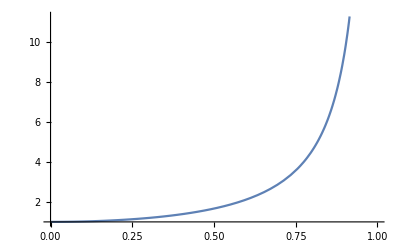

```mathematica
Plot[PairCross,{z,0,1}]
```

```mathematica
2π PairCross
```

(2 π (z^2+1))/(1-z^2)

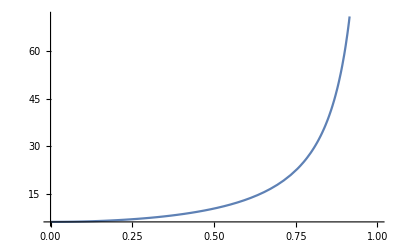

```mathematica
Plot[%,{z,0,1}]
```

```mathematica
α=1/137;
hc=389379;
```

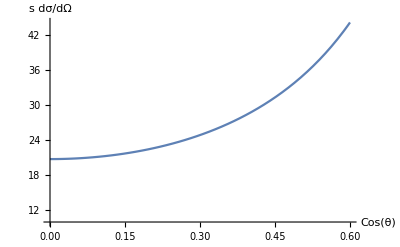

```mathematica
A=Plot[hc *α^2 PairCross,{z,0,0.6},AxesOrigin->{0,10},AxesLabel->{"Cos(θ)" , "s dσ/dΩ"}]
```

```mathematica
TableForm[{{0.0125,21.0},{0.0375,20.6},{0.0625,20.2},{0.0875,20.2},{0.1125,21.3},{0.1375,21.4},{0.1625,21.6},{0.1875,21.5},{0.2125,22.4},{0.2375,22.7},{0.2625,23.5},{0.2875,24.4},{0.3125,23.8},{0.3375,26.5},{0.3625,27.9},{0.3875,27.9},{0.4125,30.1},{0.4375,33.2},{0.4625,32.5},{0.4875,33.5},{0.5125,37.3},{0.5375,38.6}},TableHeadings->{None,{"Cos(θ)","s dσ/dΩ"}}]
```

Cos(θ) | s dσ/dΩ
0.0125 | 21.
0.0375 | 20.6
0.0625 | 20.2
0.0875 | 20.2
0.1125 | 21.3
0.1375 | 21.4
0.1625 | 21.6
0.1875 | 21.5
0.2125 | 22.4
0.2375 | 22.7
0.2625 | 23.5
0.2875 | 24.4
0.3125 | 23.8
0.3375 | 26.5
0.3625 | 27.9
0.3875 | 27.9
0.4125 | 30.1
0.4375 | 33.2
0.4625 | 32.5
0.4875 | 33.5
0.5125 | 37.3
0.5375 | 38.6

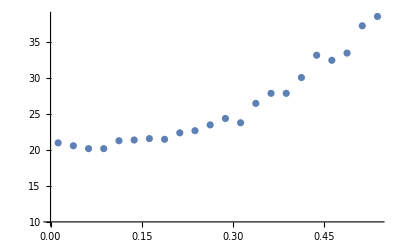

```mathematica
B=ListPlot[%,AxesOrigin->{0,10}]
```

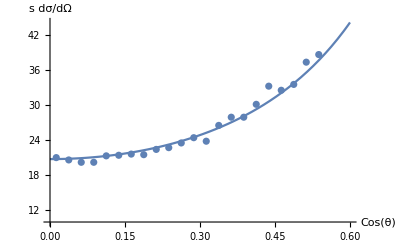

```mathematica
Show[A,B]
```

## Scratch

```mathematica
sqAmpPairAnniAllmassless= (masslessElectronssqAmpPairAnni/. {SMP["m_γ"] -> 0})//FullSimplify
```

1/(2 t^2 u^2)(2 u ((ε̄)^*(k)·(ε̄)^*(k')) (ε̄(k)·ε̄(k')) t^3+2 (k̄·(ε̄)^*(k)) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·ε̄(k')) t^3-4 ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·ε̄(k')) t^3+2 (k̄·(ε̄)^*(k)) (ε̄(k)·ε̄(k')) ((ε̄)^*(k')·OverBar[p']) t^3-2 ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·ε̄(k')) ((ε̄)^*(k')·OverBar[p']) t^3+2 ((ε̄)^*(k)·ε̄(k')) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[p']) t^3+2 s (k̄·(ε̄)^*(k)) (k̄·(ε̄)^*(k')) (ε̄(k)·ε̄(k')) t^2+2 u (k̄·(ε̄)^*(k')) (p̄·(ε̄)^*(k)) (ε̄(k)·ε̄(k')) t^2+2 u (k̄·(ε̄)^*(k)) (p̄·(ε̄)^*(k')) (ε̄(k)·ε̄(k')) t^2-2 s (k̄·(ε̄)^*(k')) ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·ε̄(k')) t^2-4 u (p̄·(ε̄)^*(k')) ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·ε̄(k')) t^2+4 (k̄·(ε̄)^*(k)) (k̄·(ε̄)^*(k')) (p̄·ε̄(k')) (ε̄(k)·OverBar[p']) t^2-4 u (p̄·ε̄(k')) ((ε̄)^*(k)·(ε̄)^*(k')) (ε̄(k)·OverBar[p']) t^2+2 s (k̄·(ε̄)^*(k')) ((ε̄)^*(k)·ε̄(k')) (ε̄(k)·OverBar[p']) t^2-8 (k̄·(ε̄)^*(k')) (p̄·ε̄(k')) ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·OverBar[p']) t^2+2 s (k̄·(ε̄)^*(k)) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·ε̄(k')) t^2-4 s ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·ε̄(k')) t^2+2 u ((ε̄)^*(k)·ε̄(k')) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[k']) t^2+2 u ((ε̄)^*(k)·OverBar[k']) (ε̄(k)·ε̄(k')) ((ε̄)^*(k')·OverBar[p']) t^2-2 u ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·ε̄(k')) ((ε̄)^*(k')·OverBar[p']) t^2-4 (k̄·(ε̄)^*(k)) (p̄·ε̄(k')) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[p']) t^2-2 u ((ε̄)^*(k)·ε̄(k')) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[p']) t^2+8 (p̄·ε̄(k')) ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[p']) t^2+2 u ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·(ε̄)^*(k')) (ε̄(k')·OverBar[k']) t^2-2 u ((ε̄)^*(k)·ε̄(k)) ((ε̄)^*(k')·OverBar[p']) (ε̄(k')·OverBar[k']) t^2-s^2 u ((ε̄)^*(k)·ε̄(k')) (ε̄(k)·(ε̄)^*(k')) t+2 s u (p̄·ε̄(k')) ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·(ε̄)^*(k')) t+2 u^3 ((ε̄)^*(k)·(ε̄)^*(k')) (ε̄(k)·ε̄(k')) t-s^2 u ((ε̄)^*(k)·(ε̄)^*(k')) (ε̄(k)·ε̄(k')) t+2 s u (k̄·(ε̄)^*(k')) ((ε̄)^*(k)·OverBar[k']) (ε̄(k)·ε̄(k')) t+2 u^2 (p̄·(ε̄)^*(k')) ((ε̄)^*(k)·OverBar[k']) (ε̄(k)·ε̄(k')) t+2 u^2 (k̄·(ε̄)^*(k')) ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·ε̄(k')) t+2 u^2 (p̄·ε̄(k')) ((ε̄)^*(k)·(ε̄)^*(k')) (ε̄(k)·OverBar[k']) t+2 s u (p̄·(ε̄)^*(k')) ((ε̄)^*(k)·ε̄(k')) (ε̄(k)·OverBar[p']) t+s^2 u ((ε̄)^*(k)·ε̄(k)) ((ε̄)^*(k')·ε̄(k')) t-2 s u (p̄·ε̄(k)) ((ε̄)^*(k)·OverBar[p']) ((ε̄)^*(k')·ε̄(k')) t-2 s u (k̄·(ε̄)^*(k)) (ε̄(k)·OverBar[k']) ((ε̄)^*(k')·ε̄(k')) t+2 s u ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·OverBar[k']) ((ε̄)^*(k')·ε̄(k')) t-2 u^2 (k̄·(ε̄)^*(k)) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·ε̄(k')) t-2 s u (p̄·(ε̄)^*(k)) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·ε̄(k')) t+2 s u ((ε̄)^*(k)·OverBar[k']) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·ε̄(k')) t+4 u^2 ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·ε̄(k')) t+2 s u (k̄·(ε̄)^*(k)) (ε̄(k)·ε̄(k')) ((ε̄)^*(k')·OverBar[k']) t+2 u^2 (p̄·(ε̄)^*(k)) (ε̄(k)·ε̄(k')) ((ε̄)^*(k')·OverBar[k']) t-2 s u ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·ε̄(k')) ((ε̄)^*(k')·OverBar[k']) t+2 s u ((ε̄)^*(k)·ε̄(k')) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[k']) t-2 s u (p̄·ε̄(k')) ((ε̄)^*(k)·ε̄(k)) ((ε̄)^*(k')·OverBar[p']) t+2 s u (p̄·ε̄(k)) ((ε̄)^*(k)·ε̄(k')) ((ε̄)^*(k')·OverBar[p']) t-2 s u (k̄·(ε̄)^*(k)) (ε̄(k)·ε̄(k')) ((ε̄)^*(k')·OverBar[p']) t-4 u^2 (p̄·(ε̄)^*(k)) (ε̄(k)·ε̄(k')) ((ε̄)^*(k')·OverBar[p']) t-2 u^2 ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·ε̄(k')) ((ε̄)^*(k')·OverBar[p']) t+4 u (k̄·(ε̄)^*(k)) (p̄·ε̄(k')) (ε̄(k)·OverBar[k']) ((ε̄)^*(k')·OverBar[p']) t-4 u (p̄·ε̄(k')) ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·OverBar[k']) ((ε̄)^*(k')·OverBar[p']) t-4 u (k̄·(ε̄)^*(k)) (p̄·ε̄(k')) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[p']) t-2 u^2 ((ε̄)^*(k)·ε̄(k')) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[p']) t-4 s u ((ε̄)^*(k)·ε̄(k')) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[p']) t-4 u (p̄·ε̄(k')) ((ε̄)^*(k)·OverBar[k']) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[p']) t+8 u (p̄·ε̄(k')) ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[p']) t+2 (k̄·ε̄(k')) (((ε̄)^*(k)·(ε̄)^*(k')) (ε̄(k)·OverBar[p']) u^2+s ((ε̄)^*(k)·(ε̄)^*(k')) (ε̄(k)·OverBar[k']) u-s ((ε̄)^*(k)·ε̄(k)) ((ε̄)^*(k')·OverBar[k']) u+2 (p̄·(ε̄)^*(k)) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[k']) u+s t ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·(ε̄)^*(k'))-s t ((ε̄)^*(k)·(ε̄)^*(k')) (ε̄(k)·OverBar[p'])-4 t (p̄·(ε̄)^*(k')) ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·OverBar[p'])+t (k̄·(ε̄)^*(k)) (2 (p̄·(ε̄)^*(k')) (ε̄(k)·OverBar[p'])-s (ε̄(k)·(ε̄)^*(k')))+(s u ((ε̄)^*(k)·ε̄(k))+2 (t-u) (p̄·(ε̄)^*(k)) (ε̄(k)·OverBar[p'])) ((ε̄)^*(k')·OverBar[p'])+(p̄·ε̄(k)) (t u ((ε̄)^*(k)·(ε̄)^*(k'))+2 u ((ε̄)^*(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[k'])-2 ((t+u) ((ε̄)^*(k)·OverBar[p'])-t (k̄·(ε̄)^*(k))) ((ε̄)^*(k')·OverBar[p']))) t-2 s u (k̄·(ε̄)^*(k')) ((ε̄)^*(k)·ε̄(k)) (ε̄(k')·OverBar[k']) t+2 u^2 (p̄·ε̄(k)) ((ε̄)^*(k)·(ε̄)^*(k')) (ε̄(k')·OverBar[k']) t+4 u (k̄·(ε̄)^*(k')) (p̄·ε̄(k)) ((ε̄)^*(k)·OverBar[p']) (ε̄(k')·OverBar[k']) t+2 s u ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·(ε̄)^*(k')) (ε̄(k')·OverBar[k']) t+4 u (k̄·(ε̄)^*(k')) (p̄·(ε̄)^*(k)) (ε̄(k)·OverBar[p']) (ε̄(k')·OverBar[k']) t-2 s u ((ε̄)^*(k)·(ε̄)^*(k')) (ε̄(k)·OverBar[p']) (ε̄(k')·OverBar[k']) t-4 u (p̄·ε̄(k)) ((ε̄)^*(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[p']) (ε̄(k')·OverBar[k']) t-4 u (p̄·(ε̄)^*(k)) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[p']) (ε̄(k')·OverBar[k']) t+2 (k̄·ε̄(k)) (((ε̄)^*(k)·OverBar[p']) ((ε̄)^*(k')·ε̄(k')) t^2-((ε̄)^*(k)·ε̄(k')) ((ε̄)^*(k')·OverBar[p']) t^2-s (k̄·(ε̄)^*(k')) ((ε̄)^*(k)·ε̄(k')) t+s ((ε̄)^*(k)·OverBar[p']) ((ε̄)^*(k')·ε̄(k')) t+(k̄·ε̄(k')) (s ((ε̄)^*(k)·(ε̄)^*(k'))+2 (p̄·(ε̄)^*(k')) ((ε̄)^*(k)·OverBar[p'])-2 (p̄·(ε̄)^*(k)) ((ε̄)^*(k')·OverBar[p'])) t-s u ((ε̄)^*(k)·OverBar[k']) ((ε̄)^*(k')·ε̄(k'))-u^2 ((ε̄)^*(k)·OverBar[p']) ((ε̄)^*(k')·ε̄(k'))+u^2 ((ε̄)^*(k)·ε̄(k')) ((ε̄)^*(k')·OverBar[p'])+s u ((ε̄)^*(k)·ε̄(k')) ((ε̄)^*(k')·OverBar[p'])+(p̄·ε̄(k')) (t u ((ε̄)^*(k)·(ε̄)^*(k'))+2 t (k̄·(ε̄)^*(k')) ((ε̄)^*(k)·OverBar[p'])+2 (u ((ε̄)^*(k)·OverBar[k'])-(t+u) ((ε̄)^*(k)·OverBar[p'])) ((ε̄)^*(k')·OverBar[p']))+s u ((ε̄)^*(k)·(ε̄)^*(k')) (ε̄(k')·OverBar[k'])+(2 t (k̄·(ε̄)^*(k')) (p̄·(ε̄)^*(k))+(t^2-s u) ((ε̄)^*(k)·(ε̄)^*(k'))+2 (p̄·(ε̄)^*(k')) (u ((ε̄)^*(k)·OverBar[k'])-(t+u) ((ε̄)^*(k)·OverBar[p']))) (ε̄(k')·OverBar[p'])) t+2 s u^2 ((ε̄)^*(k)·OverBar[k']) (ε̄(k)·ε̄(k')) ((ε̄)^*(k')·OverBar[k'])+2 u^3 ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·ε̄(k')) ((ε̄)^*(k')·OverBar[k'])-2 s u^2 ((ε̄)^*(k)·ε̄(k')) (ε̄(k)·OverBar[k']) ((ε̄)^*(k')·OverBar[k'])+4 u^2 (p̄·ε̄(k')) ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·OverBar[k']) ((ε̄)^*(k')·OverBar[k'])-2 u^3 ((ε̄)^*(k)·ε̄(k')) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[k'])-4 u^2 (p̄·ε̄(k')) ((ε̄)^*(k)·OverBar[k']) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[k'])-2 s u^2 ((ε̄)^*(k)·OverBar[k']) (ε̄(k)·ε̄(k')) ((ε̄)^*(k')·OverBar[p'])-2 u^3 ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·ε̄(k')) ((ε̄)^*(k')·OverBar[p'])+2 s u^2 ((ε̄)^*(k)·ε̄(k')) (ε̄(k)·OverBar[k']) ((ε̄)^*(k')·OverBar[p'])-4 u^2 (p̄·ε̄(k')) ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·OverBar[k']) ((ε̄)^*(k')·OverBar[p'])+2 u^3 ((ε̄)^*(k)·ε̄(k')) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[p'])+4 u^2 (p̄·ε̄(k')) ((ε̄)^*(k)·OverBar[k']) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[p'])-2 s u^2 ((ε̄)^*(k)·OverBar[k']) (ε̄(k)·(ε̄)^*(k')) (ε̄(k')·OverBar[k'])-2 u^3 ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·(ε̄)^*(k')) (ε̄(k')·OverBar[k'])+2 s u^2 ((ε̄)^*(k)·(ε̄)^*(k')) (ε̄(k)·OverBar[k']) (ε̄(k')·OverBar[k'])-4 u^2 (p̄·(ε̄)^*(k')) ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·OverBar[k']) (ε̄(k')·OverBar[k'])+2 u^3 ((ε̄)^*(k)·(ε̄)^*(k')) (ε̄(k)·OverBar[p']) (ε̄(k')·OverBar[k'])+4 u^2 (p̄·(ε̄)^*(k')) ((ε̄)^*(k)·OverBar[k']) (ε̄(k)·OverBar[p']) (ε̄(k')·OverBar[k'])+2 u^3 ((ε̄)^*(k)·ε̄(k)) ((ε̄)^*(k')·OverBar[p']) (ε̄(k')·OverBar[k'])+2 s u^2 ((ε̄)^*(k)·ε̄(k)) ((ε̄)^*(k')·OverBar[p']) (ε̄(k')·OverBar[k'])+4 u^2 (p̄·ε̄(k)) ((ε̄)^*(k)·OverBar[k']) ((ε̄)^*(k')·OverBar[p']) (ε̄(k')·OverBar[k'])-4 u^2 (p̄·ε̄(k)) ((ε̄)^*(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[p']) (ε̄(k')·OverBar[k'])+4 u^2 (p̄·(ε̄)^*(k)) (ε̄(k)·OverBar[k']) ((ε̄)^*(k')·OverBar[p']) (ε̄(k')·OverBar[k'])-4 u^2 (p̄·(ε̄)^*(k)) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[p']) (ε̄(k')·OverBar[k'])-2 (-((ε̄)^*(k)·OverBar[p']) (ε̄(k)·(ε̄)^*(k')) t^3+((ε̄)^*(k)·(ε̄)^*(k')) (ε̄(k)·OverBar[p']) t^3+u ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·(ε̄)^*(k')) t^2-u ((ε̄)^*(k)·(ε̄)^*(k')) (ε̄(k)·OverBar[k']) t^2+u ((ε̄)^*(k)·(ε̄)^*(k')) (ε̄(k)·OverBar[p']) t^2-4 (p̄·(ε̄)^*(k')) ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·OverBar[p']) t^2+u ((ε̄)^*(k)·ε̄(k)) ((ε̄)^*(k')·OverBar[k']) t^2+s u (p̄·(ε̄)^*(k')) ((ε̄)^*(k)·ε̄(k)) t+2 u^2 (p̄·ε̄(k)) ((ε̄)^*(k)·(ε̄)^*(k')) t-s u (p̄·(ε̄)^*(k)) (ε̄(k)·(ε̄)^*(k')) t+u^2 ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·(ε̄)^*(k')) t+2 s u ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·(ε̄)^*(k')) t+2 u (p̄·(ε̄)^*(k')) ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·OverBar[k']) t+u^2 ((ε̄)^*(k)·(ε̄)^*(k')) (ε̄(k)·OverBar[p']) t+2 u (p̄·(ε̄)^*(k')) ((ε̄)^*(k)·OverBar[k']) (ε̄(k)·OverBar[p']) t-4 u (p̄·(ε̄)^*(k')) ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·OverBar[p']) t+(k̄·(ε̄)^*(k')) (-s u ((ε̄)^*(k)·ε̄(k))+2 (u-t) (p̄·ε̄(k)) ((ε̄)^*(k)·OverBar[p'])+2 (t+u) (p̄·(ε̄)^*(k)) (ε̄(k)·OverBar[p'])) t+(k̄·(ε̄)^*(k)) (2 t (k̄·(ε̄)^*(k')) (p̄·ε̄(k))+(t^2-u (s+u)) (ε̄(k)·(ε̄)^*(k'))+2 (p̄·(ε̄)^*(k')) ((t+u) (ε̄(k)·OverBar[p'])-u (ε̄(k)·OverBar[k']))) t+2 u (p̄·ε̄(k)) ((ε̄)^*(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[k']) t+2 u (p̄·(ε̄)^*(k)) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[k']) t-s u^2 ((ε̄)^*(k)·OverBar[k']) (ε̄(k)·(ε̄)^*(k'))-u^3 ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·(ε̄)^*(k'))+s u^2 ((ε̄)^*(k)·(ε̄)^*(k')) (ε̄(k)·OverBar[k'])-2 u^2 (p̄·(ε̄)^*(k')) ((ε̄)^*(k)·OverBar[p']) (ε̄(k)·OverBar[k'])+u^3 ((ε̄)^*(k)·(ε̄)^*(k')) (ε̄(k)·OverBar[p'])+2 u^2 (p̄·(ε̄)^*(k')) ((ε̄)^*(k)·OverBar[k']) (ε̄(k)·OverBar[p'])-u^3 ((ε̄)^*(k)·ε̄(k)) ((ε̄)^*(k')·OverBar[k'])-s u^2 ((ε̄)^*(k)·ε̄(k)) ((ε̄)^*(k')·OverBar[k'])-2 u^2 (p̄·ε̄(k)) ((ε̄)^*(k)·OverBar[k']) ((ε̄)^*(k')·OverBar[k'])+2 u^2 (p̄·ε̄(k)) ((ε̄)^*(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[k'])-2 u^2 (p̄·(ε̄)^*(k)) (ε̄(k)·OverBar[k']) ((ε̄)^*(k')·OverBar[k'])+2 u^2 (p̄·(ε̄)^*(k)) (ε̄(k)·OverBar[p']) ((ε̄)^*(k')·OverBar[k'])+2 u ((u (s+u)-t^2) ((ε̄)^*(k)·ε̄(k))+2 ((p̄·ε̄(k)) (u ((ε̄)^*(k)·OverBar[k'])-(t+u) ((ε̄)^*(k)·OverBar[p']))+(p̄·(ε̄)^*(k)) (u (ε̄(k)·OverBar[k'])-(t+u) (ε̄(k)·OverBar[p'])))) ((ε̄)^*(k')·OverBar[p'])) (ε̄(k')·OverBar[p'])) e^4

```mathematica
SqampKN//Expand
```

-(4 e^4 m^4)/((Eg^2-p^2 cos(θ)) (Eg^2+p^2 cos(θ)))+(2 e^4 m^4)/((Eg^2-p^2 cos(θ))^2)+(2 e^4 m^4)/((Eg^2+p^2 cos(θ))^2)-(4 e^4 m^2)/(Eg^2-p^2 cos(θ))+(4 e^4 m^2)/(Eg^2+p^2 cos(θ))+(2 e^4 Eg^2)/(Eg^2-p^2 cos(θ))+(2 e^4 p^2 cos(θ))/(Eg^2-p^2 cos(θ))+(2 e^4 Eg^2)/(Eg^2+p^2 cos(θ))-(2 e^4 p^2 cos(θ))/(Eg^2+p^2 cos(θ))

```mathematica
Collect[%,2 e^4]
```

2 e^4 (m^4/((Eg^2-p^2 cos(θ))^2)+m^4/((Eg^2+p^2 cos(θ))^2)+Eg^2/(Eg^2-p^2 cos(θ))+(p^2 cos(θ))/(Eg^2-p^2 cos(θ))+Eg^2/(Eg^2+p^2 cos(θ)))-(4 e^4 m^4)/((Eg^2-p^2 cos(θ)) (Eg^2+p^2 cos(θ)))-(4 e^4 m^2)/(Eg^2-p^2 cos(θ))+(4 e^4 m^2)/(Eg^2+p^2 cos(θ))-(2 e^4 p^2 cos(θ))/(Eg^2+p^2 cos(θ))

```mathematica
TrigReduce[Sin[θ]^2]//Distribute
```

1/2-1/2 cos(2 θ)

```mathematica
1/2-1/2 Expand[Cos[2x],Trig->True]
```

1/2 (sin^2(x)-cos^2(x))+1/2

```mathematica
TableForm[{{0.0125,21.0},{0.0375,20.6},{0.0625,20.2},{0.0875,20.2},{0.1125,21.3},{0.1375,21.4},{0.1625,21.6},{0.1875,21.5},{0.2125,22.4},{0.2375,22.7},{0.2625,23.5},{0.2875,24.4},{0.3125,23.8},{0.3375,26.5},{0.3625,27.9},{0.3875,27.9},{0.4125,30.1},{0.4375,33.2},{0.4625,32.5},{0.4875,33.5},{0.5125,37.3},{0.5375,38.6}}]
```

0.0125 | 21.
0.0375 | 20.6
0.0625 | 20.2
0.0875 | 20.2
0.1125 | 21.3
0.1375 | 21.4
0.1625 | 21.6
0.1875 | 21.5
0.2125 | 22.4
0.2375 | 22.7
0.2625 | 23.5
0.2875 | 24.4
0.3125 | 23.8
0.3375 | 26.5
0.3625 | 27.9
0.3875 | 27.9
0.4125 | 30.1
0.4375 | 33.2
0.4625 | 32.5
0.4875 | 33.5
0.5125 | 37.3
0.5375 | 38.6

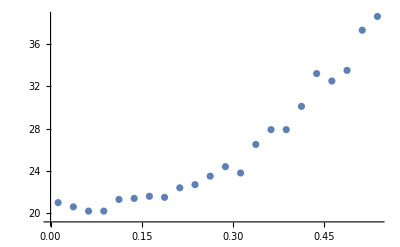

```mathematica
ListPlot[%]
```

```mathematica
Overlay[{A,B}, Alignment->Left]
```

-Graphics--Graphics-